```mathematica
Plus[3,4]
```

7

```mathematica
Times[2,3]
```

6

```mathematica
Times[2,Plus[2,3]]
```

10

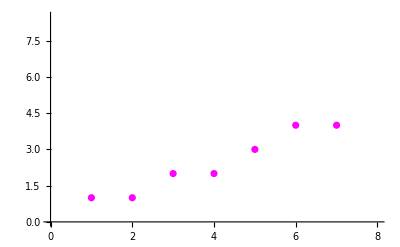

```mathematica
ListPlot[{1,1,2,2,3,4,4,88},PlotStyle->Magenta]
```

```mathematica
x = Range[88]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88}

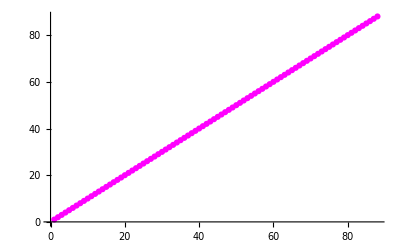

```mathematica
ListPlot[x,PlotStyle->Magenta]
```

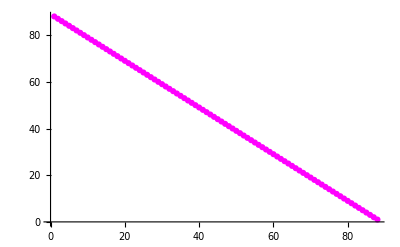

```mathematica
ListPlot[Reverse[x],PlotStyle->Magenta]
```

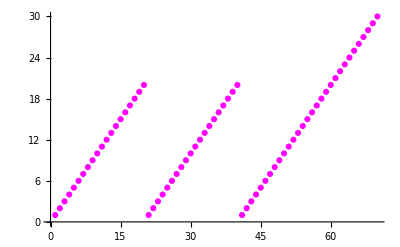

```mathematica
ListPlot[Join[Range[20],Range[20],Range[30]],PlotStyle->Magenta]
```

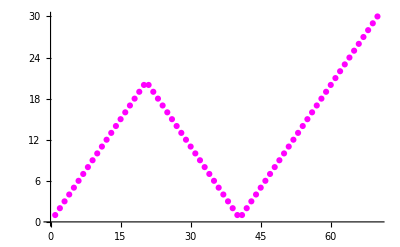

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],Range[30]],PlotStyle->Magenta]
```

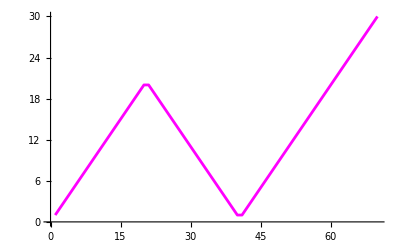

```mathematica
ListLinePlot[Join[Range[20],Reverse[Range[20]],Range[30]],PlotStyle->Magenta]
```

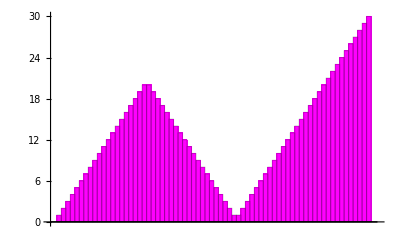

```mathematica
BarChart[Join[Range[20],Reverse[Range[20]],Range[30]],ChartStyle->Magenta]
```

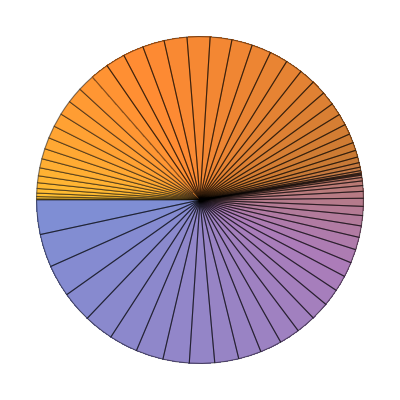

```mathematica
PieChart[Join[Range[20],Reverse[Range[20]],Range[30]],ChartStyle->"Hue[.5]"]
```

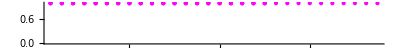

```mathematica
NumberLinePlot[Join[Range[20],Reverse[Range[20]],Range[30]],PlotStyle->Magenta]
```

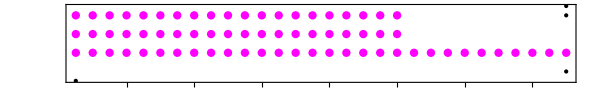

```mathematica
TimelinePlot[Join[Range[20],Reverse[Range[20]],Range[30]],PlotStyle->Magenta]
```

```mathematica
data=Table[{3+i+RandomReal[{-3,7}],i+RandomReal[{-2,5}]},{i,1,20}];
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[…]

```mathematica
model["BestFit"]
```

-0.810145+0.874127 x

```mathematica
model["BestFit"]
```

-0.810145+0.874127 x

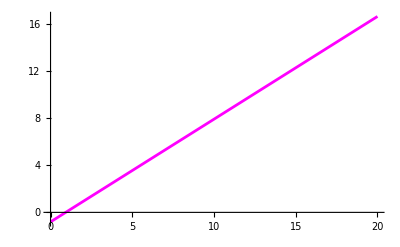

```mathematica
Plot[model["BestFit"],{x,0,20},PlotStyle->Magenta]
```

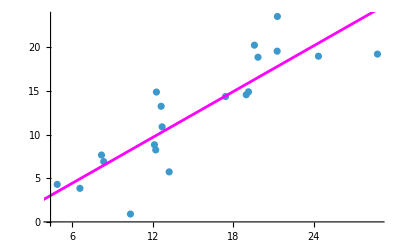

```mathematica
Show[ListPlot[data],Plot[model["BestFit"],{x,0,30},PlotStyle->Magenta]]
```

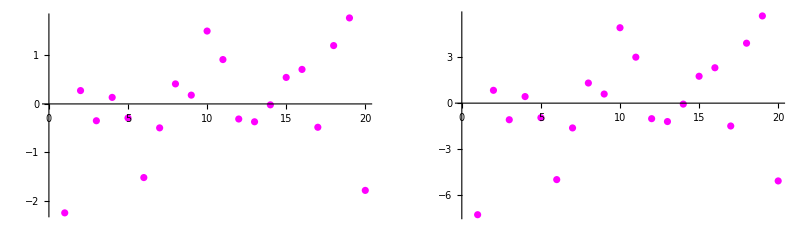

```mathematica
{sr,fr}=model[{"StandardizedResiduals","FitResiduals"}];

{{ListPlot[sr,PlotStyle->Magenta],ListPlot[fr,PlotStyle->Magenta]}}//GraphicsGrid
```

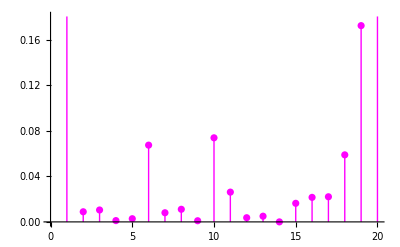

```mathematica
ListPlot[model["CookDistances"],Filling->Axis,FillingStyle->Thick,PlotStyle->Magenta]
```

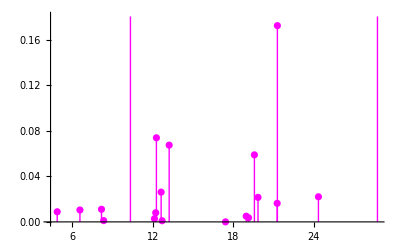

```mathematica
ListPlot[Transpose[{data[[All,1]],model["CookDistances"]}],Filling->Axis,FillingStyle->Thick,PlotStyle->Magenta]
```

```mathematica
model["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVA,BestFitAround,BestFitDataAround,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,Weights,DesignMatrix,DurbinWatsonD,Eigenstructure,EstimatedVariance,FitDifferences,FitResiduals,Function,TabularFunction,FVarianceRatios,HatDiagonal,MeanPredictions,MeanPredictionBands,ParameterEstimates,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictions,SinglePredictionBands,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
mesh=MengerMesh[2,3]
```

-Graphics3D-

```mathematica
SurfaceArea[mesh]
```

13.037

```mathematica
Integrate[y z,{x,y,z}∈mesh]
```

0.137174

```mathematica
RegionPlot3D[mesh,ColorFunction->Function[{x,y,z},Hue[Norm[{x,y,z}]]]]
```

-Graphics3D-